```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\reimplementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
SetOptions[LinTicks,TickLengthScale->1.5];
```

```mathematica
t=1.0;
J=0.4t;
shift=0.184;
pltStyle=Directive[Dashing[{0.025,0.025}],Opacity[0.7,Gray],Thickness[0.01]];
pltStyle2=Directive[Dashing[{0.0075,0.0075}],Opacity[0.7,Gray],Thickness[0.01]];
```

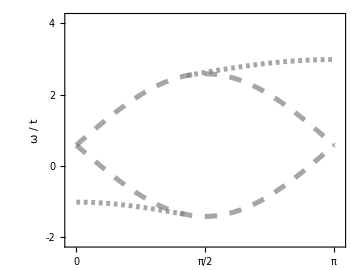

```mathematica
eye=Plot[{J+2t Sin[k],J-2t Sin[k]}+shift,{k,0,Pi},PlotStyle->pltStyle,
PlotRange->{{0-1/42,1+1/42}*Pi,{-2.15,4.15}},
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
PlotLegends->Placed[Automatic,Right],
AspectRatio->0.75,
FrameLabel->{(*"k"*)None,Style["ω / t"]},
(*Epilog->{
Text[
Style["(c)",Black,24,FontFamily->"Bookman Old Style"],
{Pi/14,3.5}]
},*)
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];
hump=Plot[{J+Sqrt[J^2+4t^2-4t J Cos[k]]}+shift,{k,3Pi/7,Pi},PlotStyle->pltStyle2,
PlotRange->{{0,Pi},{-2,6}},
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
PlotLegends->Placed[Automatic,Right],
AspectRatio->0.75,
(*FrameLabel->{"k","ω"},*)
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];
pit=Plot[{J-Sqrt[J^2+4t^2-4t J Cos[k]]}+shift,{k,0,3Pi/7},PlotStyle->pltStyle2,
PlotRange->{{0-1/28,1+1/28}*Pi,{-2,6}},
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
PlotLegends->Placed[Automatic,Right],
AspectRatio->0.75,
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];
Fig1c=Show[{eye,hump,pit},ImageSize->Medium]
Clear[t,J]
```

```mathematica
(*iA=1;
mcf=Function[x,Blend[{White,Lighter[colorScales[[iA]]],Black},x]];
bl=BarLegend[{mcf,{0,1}},LegendMarkerSize->300,LegendLayout->"Row",LabelStyle->Directive[Black,20,FontFamily->"Bookman Old Style"]]*)
```

```mathematica
Fig1x=Show[{spcPlots[[1,1,3]],Fig1c},ImageSize->Medium]
```

-Graphics-

```mathematica
fileName=StringJoin["plots/",head,"/Fig_3-a.png"];
Export[fileName,Fig1x,ImageResolution->300]
```

plots/spc/Fig_3-a.png